```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY190/sec_int_data/412nm.dat"]
```

{{1.16196,0.0283931},{1.1485,0.0246926},{1.13288,0.0161686},{1.11879,-0.0437325},{1.10986,-0.123773},{1.10188,-0.203549},{1.0953,-0.251427},{1.09118,-0.25301},{1.08898,-0.184428},{1.08844,-0.107853},{1.08969,-0.037079},{1.094,0.0156765},{1.09832,0.0244975},{1.10319,0.0465973},{1.11502,0.0350775},{1.13408,0.0576083},{1.14571,0.0306262},{1.16039,0.0465018},{1.17699,0.0511683},{1.19764,0.032564},{1.21871,0.0141001},{1.24216,0.0227395},{1.26543,0.0201947},{1.29691,0.0109399},{1.32536,-0.0151949},{1.37118,-0.0265596},{1.45421,-0.0762981}}

-0.296039+0.226002 x

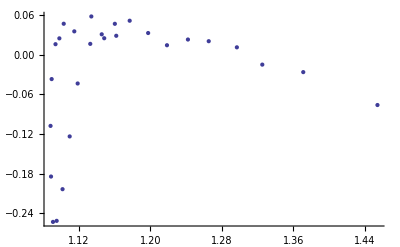

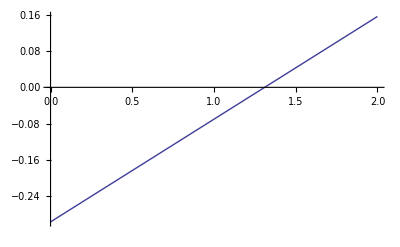

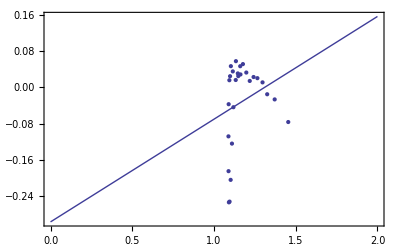

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```